```mathematica
(*1*)
DSolve[y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
(*2.a*)
DSolve[x^2*y'[x]==y[x]-y[x]x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
(*2.b*)
DSolve[{x^2*y'[x]==y[x]-y[x]x,y[1]==1/E},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
(*3.a*)
DSolve[y''[x]+5*y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
(*3.b*)
DSolve[{y''[x]+5*y'[x]+2y[x]==0,y[0]==5},y[x],x]
```

{{y[x]→5 ⅇ^((-5/2-(√17)/2) x)-ⅇ^((-5/2-(√17)/2) x) C[2]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
DSolve[{y''[x]+5*y'[x]+2y[x]==0,y[0]==10},y[x],x]
```

{{y[x]→10 ⅇ^((-5/2-(√17)/2) x)-ⅇ^((-5/2-(√17)/2) x) C[2]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
(*4*)
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0.,10.}},<>][x]}}

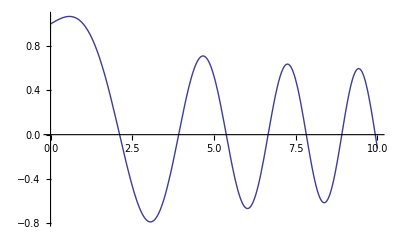

```mathematica
Plot[y[x]/.a,{x,0,10}]
```

```mathematica
(*5*)
a=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==2,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

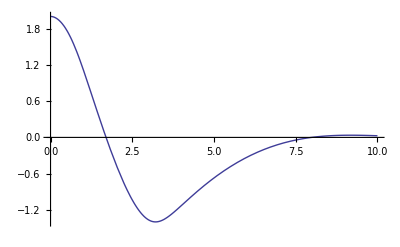

```mathematica
Plot[y[t]/.a,{t,0,10}]
```

```mathematica
(*6*)
a=NDSolve[{y''[x]+0.3*y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y[x],{x,0,30}]
```

{{y[x]→InterpolatingFunction[{{0.,30.}},<>][x]}}

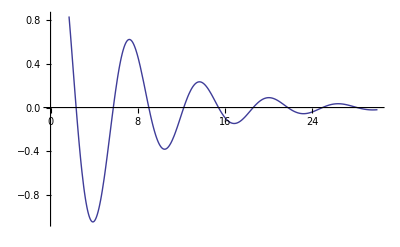

```mathematica
Plot[y[x]/.a,{x,0,30}]
```

```mathematica
(*7*)
```

```mathematica
DSolve[L*Q''[t]+R*Q'[t]+1/C*Q[t]==V*E^(j*w*t),Q[t],t]
```

{{Q[t]→-(2 C L V (√C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R-√C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) R+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)+(t (R-(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w-2 √C ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)+(t (R+(√(-4 L+C R^2))/(√C)+2 j L w))/(2 L)) j L w))/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L w) (√C R+√(-4 L+C R^2)+2 √C j L w))+ⅇ^(((-C R-√C √(-4 L+C R^2)) t)/(2 C L)) C[1]+ⅇ^(((-C R+√C √(-4 L+C R^2)) t)/(2 C L)) C[2]}}